## The Coulomb Barrier

## This is a more understandable discussion of what is on p. 50 of Reed

### Coulomb’s Law

Coulomb’s Law says the strength of the force between two charges is

F=1/(4  π ϵ_o)(|q_1||q_2|)/r^2

There are so many things to say about this simple formula!

1. It looks a lot like Newton’s Universal Theory of Gravitation, except it involves charges instead of masses. Newton’s Universal Theory of Gravitation says:

F=G(m_1 m_2)/r^2

2. Gravity always causes masses to attract. But Coulomb’s Law is different. Charges can be positive or negative. If both are positive, they repel. If both are negative, they repel. If one is positive, and one is negative, only then do they attract. That’s why there are absolute value signs around q_1 and q_2 in Coulomb’s Law, and you have to remember that “opposites attract” to get the direction of force right. 

3. Because of 2, you can see that the negative electron is attracted to the positive proton, and you can see why there might be stable orbits of the electron around the proton, and indeed, that is the picture we have of Hydrogen and all atoms.

4. Both Coulomb’s Law and Newton’s Law have a 1/r^2 factor in them. If you imagine charges as being little spheres, like teensy planets, then the r in 1/r^2 refers to the distance between the centers of the spheres.

5. The 1/r^2 factor means the force gets stronger and stronger as the charges get closer together.

6. Because of 5, you can see that there might be a great barrier in getting a proton near a nucleus, or a nucleus near a nucleus. After all, nuclei are positively charged, and the proton is positively charged, and so these objects repel each other, and the repulsion gets larger and larger as they get closer and closer.

### The Coulomb Potential

In order to be quantitative about the barrier discussed in 6, we need to introduce the the Coulomb potential. What was described on the previous page was the Coulomb force. It measures how hard the Coulomb force pushes. The Coulomb potential measures how much energy it takes to get two charges near each other.

We aren’t using calculus in this class. With calculus, it is easy to get that the potential corresponding to a 1/r^2 force goes as 1/r. E.g., the Coulomb potential is

E=1/(4  π ϵ_o)(q_1 q_2)/r

Notice the absolute value signs around the charges are gone. This says there is positive energy required to bring charges together if they are like charges, and energy is released bringing charges together if they are opposite.

I haven’t said anything about the 1/(4  π ϵ_o) out front. Don’t be intimidated. ϵ_0 is just a constant of nature whose value is about ϵ_0=8.85×10^-12 C^2/(Jm). Because it always shows up in the combination 1/(4π ϵ_0)we usually just write:

1/(4π ϵ_0)=8.99 10^9(J m)/C^2

One more thing: a Joule-meter is the same as a Newton-meter^2, and while I am at it, I might as well round 8.99 to 9, so the way I am used to seeing 1/(4π ϵ_0) written is:

1/(4π ϵ_0)=9 10^9(N m^2)/C^2

To remember why a Newton-meter is a Joule, go back to the tangerine-dropping example we did on the first day.

### Getting Reed’s Equation 2.26

If we assume that we have two nuclei colliding, then q_1=Z_1 e and q_2=Z_2 e, where e is the charge on the proton and Z as usual represents the number of protons. If we assume nucleus 1 has radius r_1 and nucleus 2 has radius r_2 then when the two spheres are just touching, their centers will be separated by r=r_1+r_2. So we put those three facts into:

E=1/(4  π ϵ_o)(q_1 q_2)/r=1/(4  π ϵ_o)((Z_1 e)(Z_2 e))/(r_1+r_2)

Reed also introduces the empirical assumption (Equation 2.25) that the volume of a nucleus is proportional to its A value (the number of nucleons which means the number of protons plus neutrons).

So we have

Volume of nucleus=4/3 π a_0^3 A=4/3 π (a_0 A^(1/3))^3

a_0 A^(1/3) has the interpretation of being the radius of the nucleus. The value of a_0 that makes this empirical formula work is a_0=1.2 10^-15 m.

So we have r_1=a_0 A_1^(1/3) and r_2=a_0 A_2^(1/3) and we put that into 

E=1/(4  π ϵ_o)((Z_1 e)(Z_2 e))/(r_1+r_2)=1/(4  π ϵ_o)((Z_1 e)(Z_2 e))/(a_0 A_1^(1/3)+a_0 A_2^(1/3)) 

and simplify and we get exactly what Reed got in Equation 2.26:

E=the Coulomb barrier =e^2/(4  π ϵ_o a_0)(Z_1 Z_2)/(A_1^(1/3)+A_2^(1/3)) 

This is how much energy it takes to get two nuclei to touch.

The mess out front is is something that can be calculated once and for all:

e^2/(4  π ϵ_o a_0)=1.6022 10^-15 J=1.2MeV

### The relationship between a 1/r^2 force and a 1/r potential

Although we aren’t using calculus in this class, it would be awfully nice to see why a 1/r^2 force creates a 1/r potential. Here is a graph of a force that is (1 N m^2)/r^2:

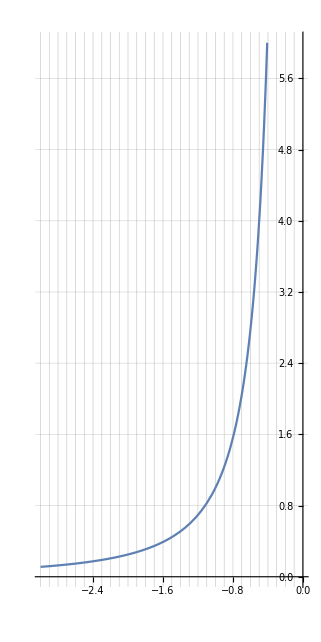

```mathematica
Plot[1/r^2, {r, -3, 0}, PlotRange->{{-3.0, 0.0}, {0.0, 6}},GridLines->{Range[-3.0, 0.0, 0.1], Range[0.0, 6, 0.1]}, AspectRatio->6/3]
```

On the horizontal axis is distance in meters, counting down from -∞ to 0. On the vertical axis is the strength of the force in Newtons. Obviously this function is hard to graph. The force gets enormously large as you get closer and closer to zero distance. It never goes to zero no matter how far to the left we plotted it. That just means the force gets weaker and weaker but never vanishes going to the left.

Now we want to get the potential. Energy is force times distance. Although the force is constantly changing, we can estimate the force times the distance, by counting up the little squares. Each square is 0.1m across and 0.1N high. So each square represents 0.01J of energy. The amount of energy required to bring the charge in from -∞ is cumulative. Fill in the following table by counting squares.

```mathematica
TableForm[Table[If[d==-3.5,{"distance", "squares", "squares x 0.01 (cumulative)"},{d, " ______","          _____"}], {d, -3.5, -0.5, 0.5}]]
```

distance | squares | squares x 0.01 (cumulative)
-3. |  ______ |           _____
-2.5 |  ______ |           _____
-2. |  ______ |           _____
-1.5 |  ______ |           _____
-1. |  ______ |           _____
-0.5 |  ______ |           _____

I will tell you the first entry in the table which results in counting up all the squares from -∞ to -3.0. It is 33.

Now you estimate the number of squares between -3.0 and -2.5, multiply by 0.01 and add it to 0.33.

You will have to do your best estimate partial squares.

Finally, after we have done all the counting and cumulative adding, we will add a fourth column to the table, and hopefully a pleasant surprise will happen.